```mathematica
ClearAll["Global'*"];
$PrePrint = MatrixForm;
```

```mathematica
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y)
rho0y[y_]:=(rho0 )(*+ 0.1 Sin[2Pi y / 20])*)
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])
xi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=1+H t- 2 Pi G rho0 t^2   (*czynnik skali dla rho0y = const*)
xiDy[y_,t_]:=(1+H t-2Pi G rho0y[y] t^2)
xiDt[y_,t_]:=(v0[y]-4Pi G m[y]t)

rhokt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k xi[y,t]],{y,-ymax,ymax}]
)

vkt[k_,t_]:=(
NIntegrate[xiDt[y,t]Exp[-I k xi[y,t]]xiDy[y,t],{y,-ymax,ymax}]
)

rhoScaledkt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k / a[t]   xi[y,t]],{y,-ymax,ymax}])
```

```mathematica
tmax=Max[t/.{Solve[xi[-ymax,t]==0,t][[2]],Solve[xi[ymax,t]==0,t][[2]]}] (*Max z czasu zapadania obu końców*)
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}]
amax=FindMaximum[a[t],{t,tmax/2}][[1]]
tstep=.05;
ts=Table[t,{t,0,tmax,tstep}];
k=1;
rhoScaledk1=rhoScaledkt[k,ts];
(*rhok1=rhokt[k,ts];
vk1=vkt[k,ts];*)
```

16.8595

7.95775

4.97887

```mathematica
(*Wykresy pierwszego modu przeskalowanej transformaty gęstości*)
ListLinePlot[Thread[{ts,Re[rhoScaledk1]}],PlotLabels->{"Re"}, PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhoScaledk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhoScaledk1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Wyresy pierwszego modu transformat gęstości i prędkości*)
(*tym czasowo nieliczone - trzeba odkomentować rhok1 i vk1*)
ListLinePlot[Thread[{ts,Re[rhok1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhok1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhok1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Re[vk1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
ListLinePlot[Thread[{ts,Im[vk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
```

```mathematica
(*Wykres xi*)
Plot3D[xi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->{"y","t"}]
```

-Graphics3D-

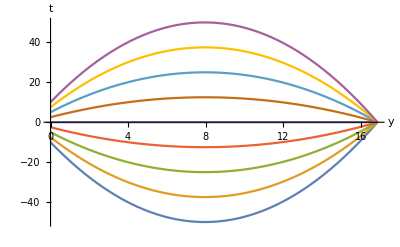

```mathematica
(*Trajektorie*)
ysToPlot=Table[y,{y,-ymax,ymax,2.5}];
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax},AxesLabel->{"y","t"}]
```

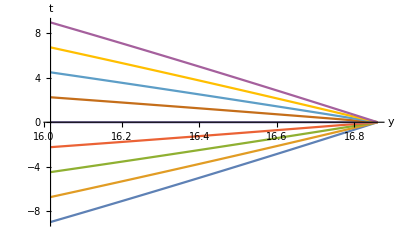

```mathematica
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,tmax*.95,tmax},AxesLabel->{"y","t"}]
```

```mathematica
(*wykres przeskalowanej gęstości: rho[x/a[t],t] dla rho[y]=rho0 *)
rhotxScaled[x_,t_]:=(rho0y[(x/a[t])/a[t]]Abs[xiDy[(xScaled/a[t])/a[t] ,t]]^(-1))
Plot3D[rhotxScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-